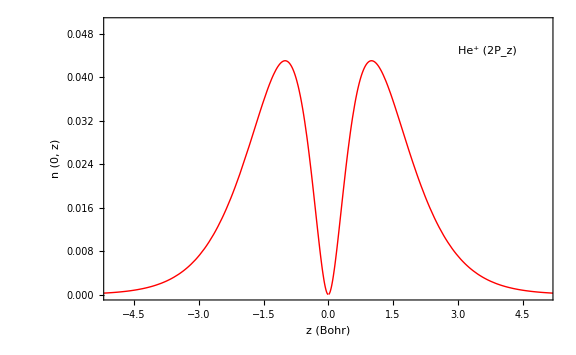

```mathematica
align[Right]={1,0};
align[Center]={0,0};(*default*)
align[Left]={-1,0};

(*lText=Text["He^+ (2P_z)",{3,0.045},align[Left],FormatType->StandardForm,BaseStyle->{FontWeight-> Bold,FontSize -> 15} ];*)
(*cText=Text["Centered",{3,0.045},align[Center]];
rText=Text["Right Aligned",{3,0.045},align[Right]];*)
ticks[min_,max_]:=Table[If[FractionalPart[i]==0.,{i,i,.06,Red},{i,"",.02,Blue}],{i,Floor[min],Ceiling[max],0.1}];
(*txt=Graphics[{lText}];*)
plot=Plot[((1/Pi))*z^2 Exp[-2*Sqrt[z^2]],{z,-10,10},PlotRange->{{-5,5},{0,0.05}},PlotStyle->{Thick,Red,Solid},Frame->True, FrameStyle->Directive[Black,Thick],FrameLabel->{"z (Bohr)","n (0, z)",None,None},FrameTicks->{{True,None},{True,None}},FrameTicksStyle->Directive[ Black,20,Ticks-> True], LabelStyle->Directive[ FontSize-> 20 ,Thick],ImageSize->Large,BaseStyle->Directive[FontFamily-> "Times"],Axes->False];

Show[plot,txt]
```

```mathematica
Export["C:\\Users\\tug12\\Dropbox\\combined flosic\\plots\\he+2pz.tiff",%862,"TIFF"]
```

C:\Users\tug12\Dropbox\combined flosic\plots\he+2pz.tiff

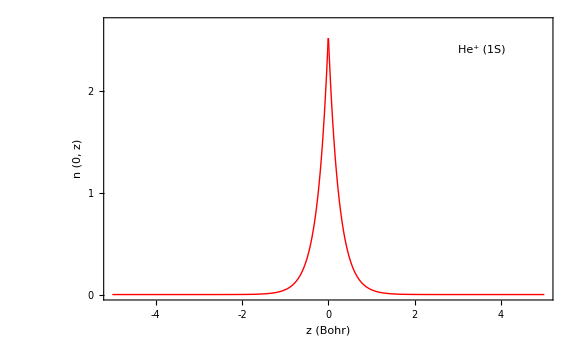

```mathematica
plot=Plot[(8/Pi)*Exp[-4*Sqrt[z^2]],{z,-5,5},PlotRange->{{-5,5},{0,02.66}},PlotStyle->{Thick,Red,Solid},Frame->True,FrameStyle->Directive[Black,15],FrameLabel->{"z (Bohr)","n (0, z)",None,None},LabelStyle->Directive[ FontSize-> 20 ,Bold,Thick],Axes->False,ImageSize->Large ,FrameTicks->{{{0,1,2},None},{{-4,-2,0,2,4},None}},
BaseStyle->Directive[FontFamily-> "Times"],Axes->False ];
align[Right]={1,0};
align[Center]={0,0};(*default*)
align[Left]={-1,0};

lText=Text["He^+ (1S)",{3,2.4},align[Left],FormatType->StandardForm,BaseStyle->{FontWeight-> Bold,FontSize -> 15} ];
(*cText=Text["Centered",{3,0.045},align[Center]];
rText=Text["Right Aligned",{3,0.045},align[Right]];*)

txt=Graphics[{lText}];
Show[plot,txt]
```

```mathematica
Integrate[(8/Pi)*Exp[-4*Sqrt[z^2]],{z,-Infinity,Infinity}]
```

4/π

```mathematica
N[4/π]
```

1.27324

```mathematica
N[(4 (1-1/ⅇ^16))/π]
```

1.27324

```mathematica
Integrate[(2/Pi)*z^2 Exp[-Sqrt[z^2]],{z,-Infinity,Infinity}]
```

8/π

```mathematica
Integrate[32*Exp[-4*r]*r^2,{r,0,Infinity}]
```

1

```mathematica
Integrate[Sin[x]*(Cos[x])^2,{x,0,Pi}]
```

2/3

```mathematica
Integrate[Abs[Exp[-ra]*Exp[-Sqrt[(4^2+ra^2-2*4*ra*Cos[theta])]]],{ra,0,Infinity},{theta,0,Pi}]
```

```mathematica
∫_0^∞ ∫_0^π ⅇ^(-ra-√(16+ra^2-8 ra Cos[theta]))ⅆthetaⅆra
NIntegrate[Abs[Exp[-ra]*Exp[-Sqrt[(4^2+ra^2-2*4*ra*Cos[theta])]]],{ra,0,Infinity},{theta,0,Pi}]
```

∫_0^∞ ∫_0^π ⅇ^(-ra-√(16+ra^2-8 ra Cos[theta]))ⅆthetaⅆra

0.0784361

```mathematica
phia[ra_]:=Exp[-ra];
phib[ra_,theta_]:=Exp[-Sqrt[(4^2+ra^2-2*4*ra*Cos[theta])]];
```

```mathematica
Simplify[(Abs[Exp[-ra]])^2+(Abs[Exp[-Sqrt[(4^2+ra^2-2*4*ra*Cos[theta])]]])^2+2*Abs[Exp[-ra]*Exp[-Sqrt[(4^2+ra^2-2*4*ra*Cos[theta])]]]]
```

ⅇ^(-2 Re[ra])+ⅇ^(-2 Re[√(16+ra^2-8 ra Cos[theta])])+2 ⅇ^(-Re[ra+√(16+ra^2-8 ra Cos[theta])])

```mathematica
Plot[1/(2*(1+.0784361))*((Exp[-2*ra])+(Exp[-Sqrt[2*(4^2+ra^2-2*4*ra*Cos[theta])]])+2*Exp[-ra]*Exp[-Sqrt[(4^2+ra^2-2*4*ra*Cos[theta])]])
,{theta,0,Pi}]
```

SphericalPlot3D::argrx: SphericalPlot3D called with 2 arguments; 3 arguments are expected.

SphericalPlot3D[(Exp[-2 ra]+Exp[-√(2 (4^2+ra^2-2 4 ra Cos[theta]))]+2 Exp[-ra] Exp[-√(4^2+ra^2-2 4 ra Cos[theta])])/(2 (1+0.0784361)),{theta,0,π}]

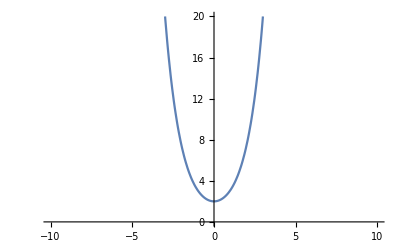

```mathematica
Plot[Exp[z]+Exp[-z],{z,-10,10},PlotRange->{{-10,10},{0,20}}]
```

```mathematica
Integrate[1/(16*Pi)*r^4*Exp[-r]*(Cos[theta])^2*Sin[theta]*2*Pi,{theta,0,Pi},{r,0,Infinity}]
```

2

```mathematica
Integrate[1/Pi*r^4*Exp[-2r]*(Cos[theta])^2*Sin[theta]*2*Pi,{theta,0,Pi},{r,0,Infinity}]
```

1

```mathematica
RegionPlot[1/(2*(1+.0784361))*((Exp[-2*ra])+(Exp[-Sqrt[2*(4^2+ra^2-2*4*ra*Cos[theta])]])+2*Exp[-ra]*Exp[-Sqrt[(4^2+ra^2-2*4*ra*Cos[theta])]]),"ZStackedPlanes",{ra,-2,2},{theta,-2,2}]
```

RegionPlot::nonopt: Options expected (instead of {theta,-2,2}) beyond position 3 in RegionPlot[(Exp[-2 ra]+Exp[-√(2 Plus[«3»])]+2 Exp[-ra] Exp[-√Plus[«3»]])/(2 (1+0.0784361)),ZStackedPlanes,{ra,-2,2},{theta,-2,2}]. An option must be a rule or a list of rules.

RegionPlot[(Exp[-2 ra]+Exp[-√(2 (4^2+ra^2-2 4 ra Cos[theta]))]+2 Exp[-ra] Exp[-√(4^2+ra^2-2 4 ra Cos[theta])])/(2 (1+0.0784361)),ZStackedPlanes,{ra,-2,2},{theta,-2,2}]

-Graphics3D-

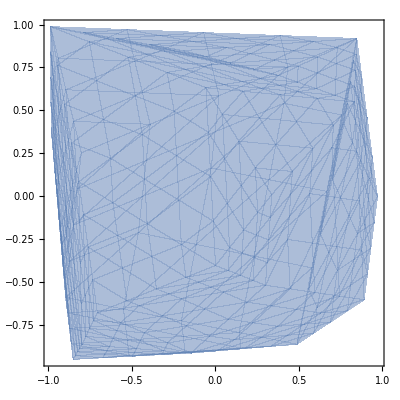

```mathematica
rr=ConvexHullMesh[RandomReal[{-1,1},{50,3}]]
RegionPlot[rr]
```

```mathematica
Integrate[8/Pi*Exp[-4*r]*4*Pi*r^2,{r,0,Infinity}]
```

1

```mathematica
Abs[Grad[Exp[-r],{r,θ.ϕ}]]
```

{ⅇ^(-Re[r]),0}

```mathematica
Plot3D[((1/Pi))*z^2 Exp[-2*Sqrt[x^2+y^2+z^2]],{x,-10,10},{y,-10,10},{z,-10,10}]
```

Plot3D::nonopt: Options expected (instead of {z,-10,10}) beyond position 3 in Plot3D[(z^2 Exp[-2 √(x^2+y^2+z^2)])/π,{x,-10,10},{y,-10,10},{z,-10,10}]. An option must be a rule or a list of rules.

Plot3D[(z^2 Exp[-2 √(x^2+y^2+z^2)])/π,{x,-10,10},{y,-10,10},{z,-10,10}]

```mathematica
Maximize[(ⅇ^(-2 r) r^2 Cos[θ]^2)/π,{r,θ}]
```

```mathematica
n[z_]:=1/Pi*z^2*Exp[-2*Sqrt[z^2]]
Evaluate[n[1]]
```

1/(ⅇ^2 π)

```mathematica
N[1/(ⅇ^2 π)]
```

0.0430786

```mathematica
N[4/(ⅇ^4 π)]
```

0.0233202

```mathematica
N[1/(ⅇ^2 π)]
```

```mathematica
SliceContourPlot3D[((1/Pi))*z^2 Exp[-2*Sqrt[x^2+y^2+z^2]],{x,-4,4},{y,-4,4},{z,-4,4}]
```

-Graphics3D-

```mathematica
SliceContourPlot3D[(z^2 Exp[-2 √(x^2+y^2+z^2)])/π,{x,-4,4},{y,-4,4},{z,-4,4},PlotTheme->Automatic]
```

-Graphics3D-

```mathematica
{{-5,-4,-3,-2,-1,0,1,2,3,4,5,{0.5,Spacer[0]},{1.5,Spacer[0]},{2.5,Spacer[0]},{3.5,Spacer[0]},{4.5,Spacer[0]},{-0.5,Spacer[0]},{-1.5,Spacer[0]},{-2.5,Spacer[0]},{-3.5,Spacer[0]},{-4.5,Spacer[0]}},Automatic}
```

```mathematica
ClearAll
plot=Plot[((1/Pi))*z^2 Exp[-2*Sqrt[z^2]],{z,-10,10},PlotRange->{{-5,5},{0,0.05}},PlotStyle->{Thick,Red,Solid},Frame->True, FrameStyle->Directive[Black,Thick],FrameLabel->{"z (Bohr)","n (0, z)",None,None},FrameTicks->{{True,None},{True,None}},FrameTicksStyle->Directive[ Black,20,Ticks-> True], LabelStyle->Directive[ FontSize-> 20 ,Thick],ImageSize->Large,BaseStyle->Directive[FontFamily-> "Times"],Axes->False];

Show[plot,txt]
```

ClearAll

-Graphics-